### The Bath: Ohmic

The Bath Spectral function

```mathematica
J[w_]:=w*Exp[-(w/s)^2]
```

The Imaginary part of \Sigma^R is then given by,

```mathematica
ImSigma[w_]=-J[w]
```

-ⅇ^(-w^2/s^2) w

The Real Part is then obtained by Kramers-Kronig Relations,

```mathematica
Integrate[(2/Pi)*a *ImSigma[a]/(a^2-w^2),{a,0,∞}, PrincipalValue->True]
```

ConditionalExpression[(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s),(w∈Reals||Re[w]==0)&&w^2∈Reals&&w≠0&&(Re[w]≠0||w∉Reals)&&Re[s^2]≥0]

```mathematica
ReSigma[w_]:=(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s)
```

```mathematica
SigmaR[w_]:= L*(ReSigma[w]+I *ImSigma[w])
```

```mathematica
SigmaR[a]
```

L (-ⅈ a ⅇ^(-a^2/s^2)+(-s+2 a DawsonF[a/s])/(√π √(1/s^2) s))

```mathematica
InverseFourierTransform[SigmaR[w],w,t,FourierParameters->{1, 1}]
```

-(ⅇ^(-1/4 s^2 t^2) L √(1/s^2) s^4 t)/(4 √π)-(L DiracDelta[t])/(√π √(1/s^2))-(ⅇ^(-1/4 s^2 t^2) L s^3 t Sign[t])/(4 √π)+(ⅇ^(-1/4 s^2 t^2) L s Sign'[t])/(2 √π)

```mathematica
%13/.{t->3}
```

-(3 ⅇ^(-(9 s^2)/4) L s^3)/(4 √π)-(3 ⅇ^(-(9 s^2)/4) L √(1/s^2) s^4)/(4 √π)+(ⅇ^(-(9 s^2)/4) L s Sign'[3])/(2 √π)

### Plots: some preliminary calculation

```mathematica
Simplify[-(ⅇ^(-1/4 s^2 t^2) √(1/s^2) s^4 t)/(2 √2)-(√2 DiracDelta[t])/(√(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s^3 t Sign[t])/(2 √2)+(ⅇ^(-1/4 s^2 t^2) s Sign'[t])/(√2)]
```

-(√2 DiracDelta[t])/(√(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s (√(1/s^2) s^3 t+s^2 t Sign[t]-2 Sign'[t]))/(2 √2)

```mathematica
D[(-(ⅇ^(-1/4 s^2 t^2) √(1/s^2) s^4 t)/(2 √2)-(√2 DiracDelta[t])/(√(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s^3 t Sign[t])/(2 √2)+(ⅇ^(-1/4 s^2 t^2) s Sign'[t])/(√2)), t]
```

-(ⅇ^(-1/4 s^2 t^2) √(1/s^2) s^4)/(2 √2)+(ⅇ^(-1/4 s^2 t^2) √(1/s^2) s^6 t^2)/(4 √2)-(ⅇ^(-1/4 s^2 t^2) s^3 Sign[t])/(2 √2)+(ⅇ^(-1/4 s^2 t^2) s^5 t^2 Sign[t])/(4 √2)-(√2 DiracDelta'[t])/(√(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s^3 t Sign'[t])/(√2)+(ⅇ^(-1/4 s^2 t^2) s Sign''[t])/(√2)

```mathematica
Integrate[(1/(Pi))*J[a]/(a-w),{a,-∞,∞}, PrincipalValue->True]
```

ConditionalExpression[1/π(-1/(4 √(1/s^2))ⅇ^(-w^2/s^2) (-2 ⅇ^(w^2/s^2) √π+2 π √(1/s^2) w Erfi[√(1/s^2) w]+2 √(1/s^2) w ExpIntegralEi[w^2/s^2]+√(1/s^2) w Log[1/w^2]+4 √(1/s^2) w Log[-w]-√(1/s^2) w Log[w^2])+π w MeijerG[{{-1/2,0},{-3/4,-1/4}},{{-1/2,0,0},{-3/4,-1/4}},w^2/s^2]),Re[s^2]≥0&&Re[w]<0&&Im[w]==0]

```mathematica
Simplify[%9]
```

-(√2 DiracDelta'[t])/(√(1/s^2))+1/(4 √2)ⅇ^(-1/4 s^2 t^2) (-2 √(1/s^2) s^4+√(1/s^2) s^6 t^2+s^3 (-2+s^2 t^2) Sign[t]-4 s^3 t Sign'[t]+4 s Sign''[t])

```mathematica
InverseFourierTransform[SigmaR[w],w,t, FourierParameters->{1, 1}]
```

-(ⅇ^(-1/4 s^2 t^2) √(1/s^2) s^4 t)/(4 √π)-DiracDelta[t]/(√π √(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s^3 t Sign[t])/(4 √π)+(ⅇ^(-1/4 s^2 t^2) s Sign'[t])/(2 √π)

```mathematica
Simplify[-(ⅇ^(-1/4 s^2 t^2) √(1/s^2) s^4 t)/(4 √π)-DiracDelta[t]/(√π √(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s^3 t Sign[t])/(4 √π)+(ⅇ^(-1/4 s^2 t^2) s Sign'[t])/(2 √π)]
```

-DiracDelta[t]/(√π √(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s (√(1/s^2) s^3 t+s^2 t Sign[t]-2 Sign'[t]))/(4 √π)

```mathematica
%15/.{t-> 7}
```

-(ⅇ^(-(49 s^2)/4) s (7 s^2+7 √(1/s^2) s^3-2 Sign'[7]))/(4 √π)

```mathematica
%15/.{t-> -7}
```

-(ⅇ^(-(49 s^2)/4) s (7 s^2-7 √(1/s^2) s^3-2 Sign'[-7]))/(4 √π)

```mathematica
D[(-DiracDelta[t]/(√π √(1/s^2))-(ⅇ^(-1/4 s^2 t^2) s (√(1/s^2) s^3 t+s^2 t Sign[t]-2 Sign'[t]))/(4 √π)), t]
```

-DiracDelta'[t]/(√π √(1/s^2))+(ⅇ^(-1/4 s^2 t^2) s^3 t (√(1/s^2) s^3 t+s^2 t Sign[t]-2 Sign'[t]))/(8 √π)-(ⅇ^(-1/4 s^2 t^2) s (√(1/s^2) s^3+s^2 Sign[t]+s^2 t Sign'[t]-2 Sign''[t]))/(4 √π)

```mathematica
Simplify[%16]
```

-DiracDelta'[t]/(√π √(1/s^2))+(ⅇ^(-1/4 s^2 t^2) (-2 √(1/s^2) s^4+√(1/s^2) s^6 t^2+s^3 (-2+s^2 t^2) Sign[t]-4 s^3 t Sign'[t]+4 s Sign''[t]))/(8 √π)

```mathematica
%17/.{t-> -7}
```

(ⅇ^(-(49 s^2)/4) (-2 √(1/s^2) s^4+49 √(1/s^2) s^6-s^3 (-2+49 s^2)+28 s^3 Sign'[-7]+4 s Sign''[-7]))/(8 √π)

```mathematica
FourierTransform[SigmaR[w],w,t,FourierParameters->{1, 1}]
```

1/2 ⅇ^(-1/4 s^2 t^2) √π √(1/s^2) s^4 t-(2 √π DiracDelta[t])/(√(1/s^2))-1/2 ⅇ^(-1/4 s^2 t^2) √π s^3 t Sign[t]+ⅇ^(-1/4 s^2 t^2) √π s Sign'[t]

```mathematica
DR[w_]:= 1/((w+I*n) ^2-k^2-SigmaR[w])
```

```mathematica
DR[w]
```

1/(-k^2+ⅈ ⅇ^(-w^2/s^2) w+(ⅈ n+w)^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))

```mathematica
Im[DR[w]]
```

Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) w+(ⅈ n+w)^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))]

```mathematica
Integrate[Im[DR[w]]Coth[w/2T],{w,-∞,∞}]
```

∫_(-∞)^∞ Coth[(T w)/2] Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) w+(ⅈ n+w)^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))]ⅆw

```mathematica
Integrate[Im[DR[w]]Coth[w/2T],{w,-∞,∞}, PrincipalValue->True]
```

Integrate[Coth[(T w)/2] Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) w+(ⅈ n+w)^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))],{w,-∞,∞},PrincipalValue→True]

```mathematica
Integrate[Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) *w+w^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))]Coth[w/2T],{w,-∞,∞}]
```

∫_(-∞)^∞ Coth[(T w)/2] Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) w+w^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))]ⅆw

```mathematica
Integrate[Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) *w+w^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))]Coth[w/2T],{w,-∞,∞},PrincipalValue->True]
```

Integrate[Coth[(T w)/2] Im[1/(-k^2+ⅈ ⅇ^(-w^2/s^2) w+w^2-(-s+2 w DawsonF[w/s])/(√π √(1/s^2) s))],{w,-∞,∞},PrincipalValue→True]

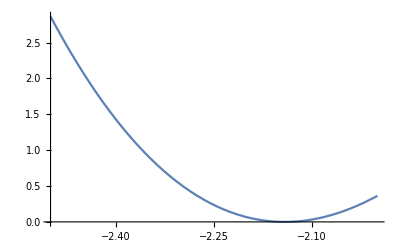

```mathematica
Plot[((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-2.5,-2},PlotRange->Full]
```

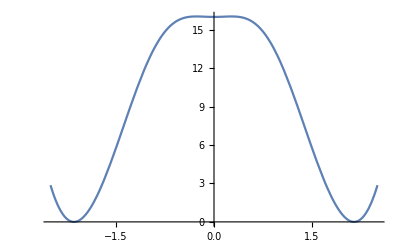

```mathematica
Plot[((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-2.5,2.5},PlotRange->Full]
```

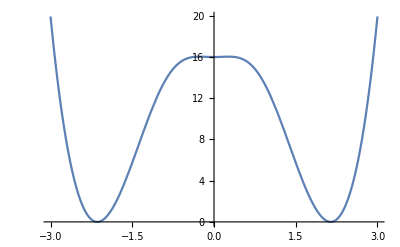

```mathematica
Plot[((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-3,3},PlotRange->Full]
```

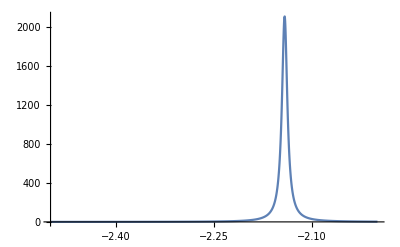

```mathematica
Plot[1/((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-2.5,-2},PlotRange->Full]
```

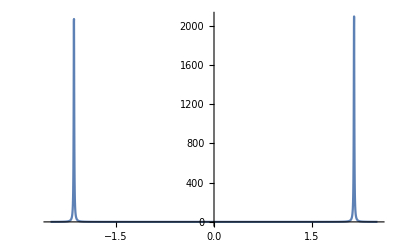

```mathematica
Plot[1/((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-2.5,2.5},PlotRange->Full]
```

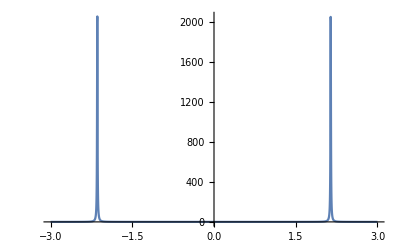

```mathematica
Plot[1/((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-3,3},PlotRange->Full]
```

```mathematica
1.586780^2
```

2.51787

```mathematica
NIntegrate[Coth[w]*(w Exp[-w^2/25])/((w^2-2.5178707684000003-(2/Sqrt[Pi])w DawsonF[w/5])^2+( w Exp[-w^2/25])^2),{w,-∞,∞}]/Pi
```

0.66187

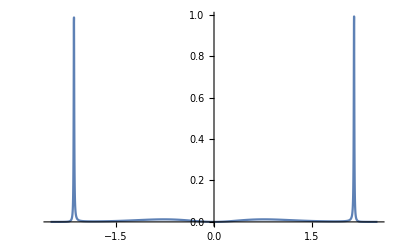

```mathematica
Plot[(w Exp[-w^2])^2/((w^2-4-w DawsonF[w])^2+( w Exp[-w^2])^2),{w,-2.5,2.5},PlotRange->Full]
```

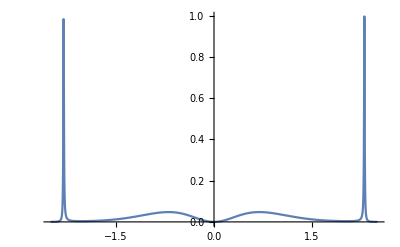

```mathematica
Plot[(2.25*w Exp[-w^2])^2/((w^2-4-2.25*w DawsonF[w])^2+( 2.25w Exp[-w^2])^2),{w,-2.5,2.5},PlotRange->Full]
```

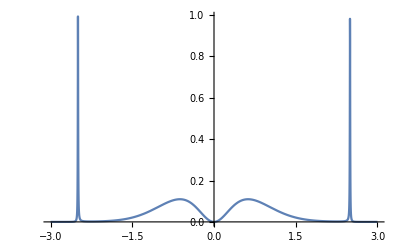

```mathematica
Plot[(4*w Exp[-w^2])^2/((w^2-4-4*w DawsonF[w])^2+( 4*w Exp[-w^2])^2),{w,-3,3},PlotRange->Full]
```

### Features of σ-λ parameter space

Features of σ-λ parameter space

```mathematica
b=10;l=0.5;
```

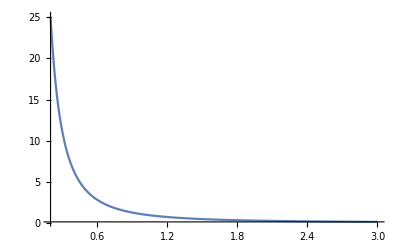

```mathematica
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0.2,3}, PlotRange->Full]
```

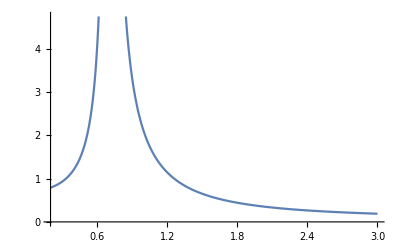

```mathematica
b=10;l=1.0;
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^(b/Sqrt[Pi])-l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0.2,3}]
```

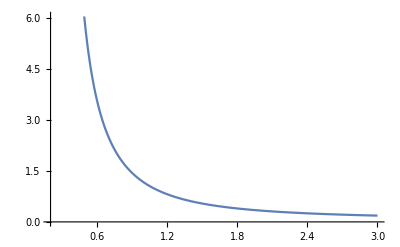

```mathematica
b=5;l=0.5;
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^(b/Sqrt[Pi])-l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0,5}]
```

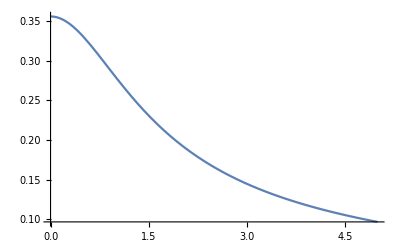

```mathematica
b=5;l=1.0;
Plot[NIntegrate[l^2*Coth[w/0.2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2-l^2*(b/Sqrt[Pi])+l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0,5}]
```

```mathematica
NIntegrate[l^2*Coth[w/0.2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2-l^2*(b/Sqrt[Pi])+l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0,5}]
```

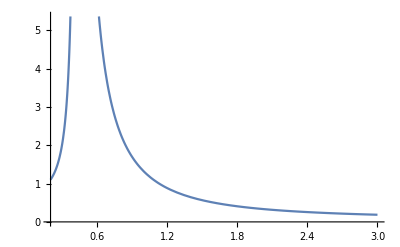

```mathematica
b=2.5;l=0.5;
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^(b/Sqrt[Pi])-l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0.2,3}]
```

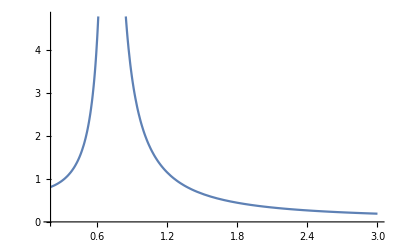

```mathematica
b=2.5;l=1.0;
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^(b/Sqrt[Pi])-l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0.2,3}, PlotRange->Full]
```

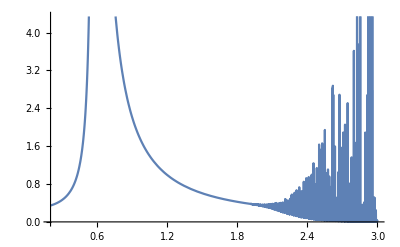

```mathematica
b=1;l=0.5;
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^(b/Sqrt[Pi])-l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0.2,3}]
```

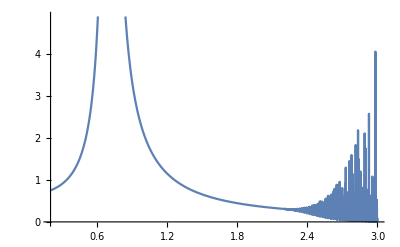

```mathematica
Plot[NIntegrate[l^2*Coth[w/2]*w Exp[-w^2/b^2]/((2*w^2-2*a^2+l^(b/Sqrt[Pi])-l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi,{a,0.2,3}]
```

### Getting the Numerical Values

```mathematica
Omega={3, 2.954471,2.819161,2.59818,2.298244,1.928469,1.50009,1.026125,0.520979};
```

```mathematica
b=2.5;l=1.0;
```

```mathematica
NIntegrate[l^2*Coth[w/1.6]*w Exp[-w^2/b^2]/((2*w^2-2*Omega^2+l^2*(2/Sqrt[Pi])w DawsonF[w/b])^2+( l^2*w Exp[-w^2/b^2])^2),{w,-∞,∞}]/Pi
```

{0.182135,0.185137,0.194758,0.213274,0.246522,0.309795,0.44917,0.85215,3.0388}

```mathematica
%46//MatrixForm
```

(0.182135
0.185137
0.194758
0.213274
0.246522
0.309795
0.44917
0.85215
3.0388)

### The Bath Functions: Non-Ohmic

The bath spectral function for a non-ohmic bath

```mathematica
J[w_]:=w^b*Exp[-(w/s)^2]
```

The Imaginary part of \Sigma^R is given by,

```mathematica
ImSigma[w_]=-J[w]
```

-ⅇ^(-w^2/s^2) w^b

The Real Part is obtained using Kramers-Cronigg Relations

```mathematica
Integrate[(2/Pi)*a *ImSigma[a]/(a^2-w^2),{a,0,∞}, PrincipalValue->True]
```

ConditionalExpression[-(ⅇ^(-w^2/s^2) (1/s^2)^(-b/2) (1/w^2)^(-b/2) (-π (1/s^2)^(b/2) Cot[(b π)/2]+π (1/w^2)^(b/2) (-w^2/s^2)^(b/2) Csc[(b π)/2]+(1/w^2)^(b/2) (-w^2/s^2)^(b/2) Gamma[1+b/2] Gamma[-b/2,-w^2/s^2]))/π,(w∈Reals||Re[w]==0)&&w^2∈Reals&&w≠0&&(Re[w]≠0||w∉Reals)&&Re[s^2]≥0&&Re[b]>-2]

```mathematica
ReSigma[w_]:=-(ⅇ^(-w^2/s^2) (1/s^2)^(-b/2) (1/w^2)^(-b/2) (-π (1/s^2)^(b/2) Cot[(b π)/2]+π (1/w^2)^(b/2) (-w^2/s^2)^(b/2) Csc[(b π)/2]+(1/w^2)^(b/2) (-w^2/s^2)^(b/2) Gamma[1+b/2] Gamma[-b/2,-w^2/s^2]))/π
```

```mathematica
SigmaR[w_]:= L*(ReSigma[w]+I *ImSigma[w])
```

```mathematica
SigmaR[a]
```

L (-ⅈ a ⅇ^(-a^2/s^2)+(-s+2 a DawsonF[a/s])/(√π √(1/s^2) s))

```mathematica
InverseFourierTransform[SigmaR[w],w,t,FourierParameters->{1, 1}]
```

-1/(8 π^(5/2))ⅈ L (1/s^2)^(-b/2) (1/(-1+ⅇ^(ⅈ b π))π^(3/2) (1/s^2)^(-1-b/2) (ⅈ b (-1+ⅇ^(ⅈ b π))^2 (1/s^2)^(b/2) t Gamma[b/2] Hypergeometric1F1[1+b/2,3/2,-1/4 s^2 t^2]+2 (4 ⅇ^((ⅈ b π)/2) (-1/s^2)^(b/2)-3 (1/s^2)^(b/2)-2 ⅇ^(ⅈ b π) (1/s^2)^(b/2)+ⅇ^(2 ⅈ b π) (1/s^2)^(b/2)) √(1/s^2) Gamma[(1+b)/2] Hypergeometric1F1[(1+b)/2,1/2,-1/4 s^2 t^2])+2^(2+b) (-1/s^2)^(b/2) (ⅈ t)^-b t^(-1-b) (ⅇ^((ⅈ b π)/2) (ⅈ t)^b-t^b) MeijerG[{{1,(2+b)/2},{}},{{(1+b)/2,(2+b)/2,(2+b)/2},{}},(s^2 t^2)/4])

```mathematica
%9/.{t->3}
```

-1/(8 π^(5/2))ⅈ L (1/s^2)^(-b/2) (1/(-1+ⅇ^(ⅈ b π))π^(3/2) (1/s^2)^(-1-b/2) (3 ⅈ b (-1+ⅇ^(ⅈ b π))^2 (1/s^2)^(b/2) Gamma[b/2] Hypergeometric1F1[1+b/2,3/2,-(9 s^2)/4]+2 (4 ⅇ^((ⅈ b π)/2) (-1/s^2)^(b/2)-3 (1/s^2)^(b/2)-2 ⅇ^(ⅈ b π) (1/s^2)^(b/2)+ⅇ^(2 ⅈ b π) (1/s^2)^(b/2)) √(1/s^2) Gamma[(1+b)/2] Hypergeometric1F1[(1+b)/2,1/2,-(9 s^2)/4])+ⅈ^-b 2^(2+b) 3^(-1-2 b) (-3^b+(3 ⅈ)^b ⅇ^((ⅈ b π)/2)) (-1/s^2)^(b/2) MeijerG[{{1,(2+b)/2},{}},{{(1+b)/2,(2+b)/2,(2+b)/2},{}},(9 s^2)/4])